```mathematica
(* Boreale method examples *)
```

```mathematica
Begin[ "BorealeTests`" ]
```

BorealeTests`

```mathematica
(* Example 3 from Boreale's 2018 paper *)
vf1={y^2, x*y};
vars1={x,y};
post1=Boreale`Post[{x-y},2,vars1,vf1]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

Done!

{x^2-y^2,x y-y^2,x-y}

```mathematica
postVariety1=FullSimplify[And@@Map[#==0&,post1],Reals]
```

x==y

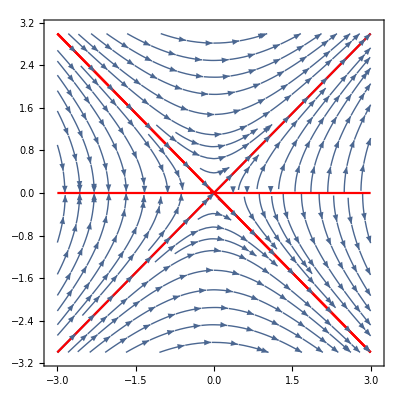

```mathematica
Show[
StreamPlot[vf1,{x,-3,3},{y,-3,3}],
ContourPlot[x-y==0,{x,-3,3},{y,-3,3}],
ContourPlot[post1==0,{x,-3,3},{y,-3,3}, ContourStyle->Red]
]
```

```mathematica
(* Example 4 from Boreale's 2018 paper *)
vf2={y^2, x*y,0,0};
vars2={x,y,x0,y0};
post2=Boreale`Post[{x-x0,y-y0},2,vars2,vf2]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

Done!

{x^2-x0^2-y^2+y0^2}

```mathematica
postVariety2=FullSimplify[And@@Map[#==0&,post2],Reals]
```

x^2+y0^2==x0^2+y^2

```mathematica
(* Collision avoidance example *)
```

```mathematica
vf3={d1,d2,e1,e2,-om1*d2,-om1*d2,-om2*e2,-om2*e1,0,0,0,0,0,0,0,0,0,0};
vars3={x1,x2,y1,y2,d1,d2,e1,e2,om1,om2,x10,x20,y10,y20,d10,d20,e10,e20};
post3=Boreale`PostUnsound[{x1-x10,x2-x20,y1-y10,y2-y20,d1-d10,d2-d20,e1-e10,e2-e20},2,vars3,vf3]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

General::stop: Further output of Solve::svars will be suppressed during this calculation.

Done!

{d1^2-d10^2-2 d10 d2-d2^2+2 d10 d20+2 d2 d20-d20^2,d1 d10-d10^2-d10 d2+d10 d20,d1 d2-d10 d2-d2^2+d2 d20,d1 d20-d10 d20-d2 d20+d20^2,d1 e1-d10 e1-d2 e1+d20 e1,d1 e10-d10 e10-d2 e10+d20 e10,d1 e2-d10 e2-d2 e2+d20 e2,d1 e20-d10 e20-d2 e20+d20 e20,d1 om1-d10 om1-d2 om1+d20 om1,d1 om2-d10 om2-d2 om2+d20 om2,d1 x1-d10 x1-d2 x1+d20 x1,d1 x10-d10 x10-d2 x10+d20 x10,d1 x2-d10 x2-d2 x2+d20 x2,d1 x20-d10 x20-d2 x20+d20 x20,d1 y1-d10 y1-d2 y1+d20 y1,d1 y10-d10 y10-d2 y10+d20 y10,d1 y2-d10 y2-d2 y2+d20 y2,d1 y20-d10 y20-d2 y20+d20 y20,d1-d10+om1 x2-om1 x20,d2-d20+om1 x2-om1 x20,e1^2-e10^2-e2^2+e20^2,e1 y1-e10 y1-e1 y10+e10 y10-e2 y2+e20 y2+e2 y20-e20 y20,-e2 y1-e20 y1+e2 y10+e20 y10+e1 y2+e10 y2-e1 y20-e10 y20,e1-e10+om2 y2-om2 y20,e2-e20+om2 y1-om2 y10}

```mathematica
post3//MatrixForm
post3//Length
```

(d1^2-d10^2-2 d10 d2-d2^2+2 d10 d20+2 d2 d20-d20^2
d1 d10-d10^2-d10 d2+d10 d20
d1 d2-d10 d2-d2^2+d2 d20
d1 d20-d10 d20-d2 d20+d20^2
d1 e1-d10 e1-d2 e1+d20 e1
d1 e10-d10 e10-d2 e10+d20 e10
d1 e2-d10 e2-d2 e2+d20 e2
d1 e20-d10 e20-d2 e20+d20 e20
d1 om1-d10 om1-d2 om1+d20 om1
d1 om2-d10 om2-d2 om2+d20 om2
d1 x1-d10 x1-d2 x1+d20 x1
d1 x10-d10 x10-d2 x10+d20 x10
d1 x2-d10 x2-d2 x2+d20 x2
d1 x20-d10 x20-d2 x20+d20 x20
d1 y1-d10 y1-d2 y1+d20 y1
d1 y10-d10 y10-d2 y10+d20 y10
d1 y2-d10 y2-d2 y2+d20 y2
d1 y20-d10 y20-d2 y20+d20 y20
d1-d10+om1 x2-om1 x20
d2-d20+om1 x2-om1 x20
e1^2-e10^2-e2^2+e20^2
e1 y1-e10 y1-e1 y10+e10 y10-e2 y2+e20 y2+e2 y20-e20 y20
-e2 y1-e20 y1+e2 y10+e20 y10+e1 y2+e10 y2-e1 y20-e10 y20
e1-e10+om2 y2-om2 y20
e2-e20+om2 y1-om2 y10)

25

```mathematica
vflimit= {(-x1-x2+x1*x2^2+x1^3),x1-x2+x1^2*x2+x2^3}/.{x1->x,x2->y};
vflimit={-α*x2+x1*(1-x1^2-x2^2)-x2*(x1^2+x2^2),α*x1+x2*(1-x1^2-x2^2) + x1*(x1^2+x2^2)+ β}/.{α->4, β->0}/.{x1->x,x2->y};
vflimit={-6 x1^2 x2+2 x1^4 x2+4 x1^2 x2^3,6 x1 x2^2-4 x1^3 x2^2-2 x1 x2^4}/.{x1->x, x2->y};
varslimit={x,y};
post4=Boreale`PostUnsound[{x+1,y-2},5,varslimit,vflimit]
```

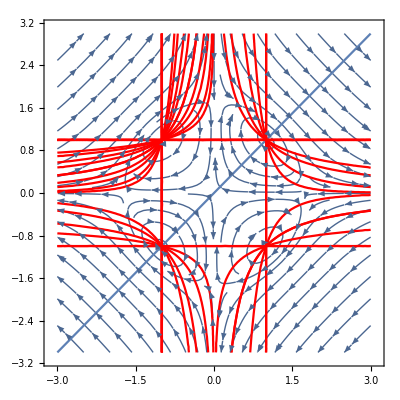

```mathematica
Show[
StreamPlot[vflimit,{x,-3,3},{y,-3,3}],
ContourPlot[x-y==0,{x,-3,3},{y,-3,3}],
ContourPlot[post4==0,{x,-3,3},{y,-3,3}, ContourStyle->Red]
]
```

```mathematica
Grad[post4[[4]],varslimit].vflimit//Simplify
```

2 x2 (x1^3+x2+2 x1^4 x2-3 x2^3+2 x2^5+x1 (-1+x2^2)+x1^2 x2 (-3+4 x2^2))

```mathematica
End[]
```

BorealeTests`